# A model for the spread of corona virus: R0

```mathematica
date=DateString[{"Day","Month","YearShort"}]
```

070420

```mathematica
AspRat=0.75;
ImSize=400;
```

## Model Parameters

## Biological parameters

```mathematica
meanhouseholdcontacts=2.15;negbinn=2;negbinp=0.15;
```

duration of the latent and infectious periods, casefatality, and ratio of transmission probabilities in 2. ring to 1. ring contacts:

```mathematica
latent=3;infectious=10;casefatality=0.02; 
transratio=0.25;declinetransm=0.5;
transmissibility=0.152;
sympconstant=4.0;gamma1=8.0;gamma2=0.7;
scenariocontactred={1.0,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.05};
```

```mathematica
calcsymp[x_]=Total[Table[Product[(1-x*sympconstant*PDF[GammaDistribution[gamma1,gamma2],j-1]),{j,2,i}]*x*sympconstant*PDF[GammaDistribution[gamma1,gamma2],i],{i,1,infectious}]];
scenarioasymptomatic=Table[FindRoot[calcsymp[x]==1-0.05*(i-1),{x,0.5}],{i,1,20}][[All,1,2]];
```

```mathematica
factorasymptomatic=scenarioasymptomatic[[1]];
```

```mathematica
contactreduction1=scenariocontactred[[1]];contactreduction2=scenariocontactred[[1]];
```

probability of leaving latent stage by time since infection:

```mathematica
probinf=Array[f,latent];
probinf=Flatten[Append[Table[0.0,{i,1,latent-3}],{0.5,0.7,1.0}]]
```

{0.5,0.7,1.}

probability of transmission per contact by time since beginning of infectious period:

```mathematica
probtransm[pt_]=Table[Min[1.0,pt*tau*Exp[-tau*declinetransm]], {tau,1,infectious}]//N;
```

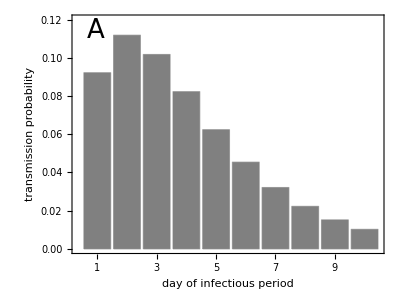

```mathematica
figure1a=Show[BarChart[probtransm[transmissibility],AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{All,{0.0,0.12}},ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}, FrameStyle->Directive[Black,17],FrameLabel->{"day of infectious period", "transmission probability"}],Graphics[Text[StyleForm["A",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,0.12*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_1A_",date,".pdf"],figure1a,"pdf"];
```

probability of developing symptoms by time since becoming infectious:

```mathematica
probsymp=Table[ factorasymptomatic*sympconstant*PDF[GammaDistribution[gamma1,gamma2],i],{i,1,infectious}];
```

```mathematica
probdevelopingsymptoms=Table[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],{i,1,infectious}];
```

```mathematica
fraccas=Total[probdevelopingsymptoms]
```

1.

```mathematica
plotprobsymptoms=BarChart[probdevelopingsymptoms, Frame->True,ChartLabels->Table[i,{i,1,infectious}],FrameLabel->{"day of infectious period", "probability symptoms"},FrameTicks->{{True,None},{True,None}},FrameStyle->Directive["Label",16]];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Probsymptoms_",date,".pdf"],plotprobsymptoms,"pdf"];
```

distribution of the number of contacts with susceptibles by time since beginning of the infectious period:

```mathematica
saturation1=Drop[Prepend[Table[Product[1-probtransm[transmissibility][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.907807,0.806282,0.724245,0.664652,0.623188,0.594891,0.575777,0.562954,0.554398}

```mathematica
saturation2=Drop[Prepend[Table[Product[1-probtransm[transmissibility*transratio][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.976952,0.949637,0.925482,0.906444,0.892307,0.882178,0.875091,0.870219,0.866913}

```mathematica
BarChart[saturation1,ChartLabels->Table[i,{i,1,infectious}]];
```

```mathematica
mu1=meanhouseholdcontacts*saturation1*contactreduction1
```

{2.15,1.95179,1.73351,1.55713,1.429,1.33985,1.27902,1.23792,1.21035,1.19196}

```mathematica
mu2=negbinn*saturation2*contactreduction2
```

{2.,1.9539,1.89927,1.85096,1.81289,1.78461,1.76436,1.75018,1.74044,1.73383}

```mathematica
contactdist1=Array[f,infectious];contactdist2=Array[f,infectious];
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}];
```

```mathematica
contact=Array[f,latent+infectious];
For [i=1,i≤infectious,i++,contact[[i]]=Mean[contactdist1[[i]]]+Mean[contactdist2[[i]]]]
```

```mathematica
numcontacts=Table[RandomVariate[contactdist1[[i]],1000]+RandomVariate[contactdist2[[i]],1000],{i,1,infectious}];
```

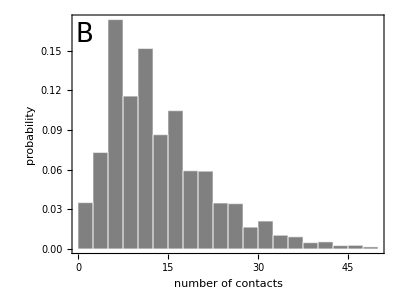

```mathematica
figure1b=Show[Histogram[RandomVariate[PoissonDistribution[meanhouseholdcontacts*contactreduction1],10000]+RandomVariate[NegativeBinomialDistribution[negbinn*contactreduction2,negbinp],10000], {0, 50, 2.5},"Probability", ChartBaseStyle->EdgeForm[White],AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"number of contacts", "probability"},FrameTicks->{{True,None},{True,None}}],Graphics[Text[StyleForm["B",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(12.0-0.5)*0.1,0.17*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_1B_",date,".pdf"],figure1b,"pdf"];
```

```mathematica
meancontacts=Table[Mean[numcontacts[[i]]],{i,1,infectious}]//N
```

{13.411,12.895,12.386,12.039,11.84,11.746,11.687,11.072,11.037,11.243}

```mathematica
plotmeancontacts=BarChart[meancontacts, ChartLabels->Table[i,{i,1,infectious}],AxesLabel->{"day infectious period","mean number of contacts with susceptibles"}];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Meancontacts_",date,".pdf"],plotmeancontacts,"pdf"];
```

```mathematica
stdcontacts=Table[StandardDeviation[numcontacts[[i]]],{i,1,infectious}]//N
```

{8.55027,8.89804,8.36223,8.43105,8.94821,8.57911,8.65066,8.1791,7.90975,8.11602}

```mathematica
ListPlot[stdcontacts];
```

basic reproduction ratio:

```mathematica
rzero[pt_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])
```

```mathematica
rzero[0.152]
```

2.50373

```mathematica
Plot[rzero[x],{x,0,0.2},GridLines->{None,{2.5}}];
```

```mathematica
rzero1[pt_]:=∑_(i=1)^infectious Mean[contactdist1[[i]]]*probtransm[pt][[i]]
```

```mathematica
rzero2[pt_, tr_]:=∑_(i=1)^infectious Mean[contactdist2[[i]]]*probtransm[tr*pt][[i]]
```

```mathematica
rzero1[transmissibility]
```

0.970251

```mathematica
rzero2[transmissibility, transratio]
```

1.53348

```mathematica
rzero1[transmissibility]+rzero2[transmissibility,transratio]
```

2.50373

```mathematica
ratiohousehold[pt_, tr_]:=rzero1[pt]/(rzero1[pt]+rzero2[pt,tr]);
```

```mathematica
ratiohousehold[transmissibility, transratio]
```

0.387522

```mathematica
rzeroday[pt_]:=Table[Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[pt][[i]]*transratio, {i,1,infectious}]
```

```mathematica
rzeroperc=rzeroday[transmissibility]/rzero[transmissibility]*100
```

{18.3497,21.0822,17.979,13.7352,9.95984,7.01482,4.84892,3.30675,2.23124,1.49233}

```mathematica
rzerocum=Table[∑_(i=1)^j rzeroperc[[i]], {j,1,infectious}];
```

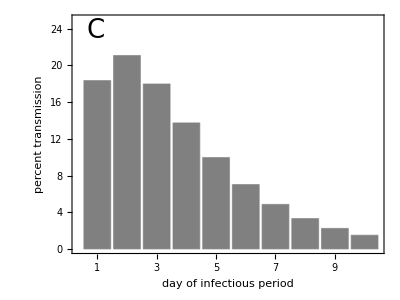

```mathematica
figure1c=Show[BarChart[rzeroperc,  AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],PlotRange->{All,{0,25}},Frame->True, FrameLabel->{"day of infectious period", "percent transmission"},FrameStyle->Directive[Black,17],  FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}],Graphics[Text[StyleForm["C",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,25*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_1C_",date,".pdf"],figure1c,"pdf"];
```

## Exponential growth rate and doubling time

```mathematica
startinf=Table[Product[(1-probinf[[k-1]]),{k,2,j}]*probinf[[j]],{j,1,latent}]
```

{0.5,0.35,0.15}

```mathematica
generations[r_,pt_]:=Sum[Sum[Exp[-r*(i+j)]*startinf[[j]](Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]),{i,1,infectious}],{j,1,latent}]
```

```mathematica
expgrowth[pt_]:=FindRoot[generations[r,pt]==1,{r,1}][[1,2]]
```

```mathematica
unconstrainedgrowth=expgrowth[transmissibility]
```

0.193233

```mathematica
doublingtime[pt_]:=Log[2]/expgrowth[pt];
```

```mathematica
unconstraineddoubtime=doublingtime[transmissibility]
```

3.58711

## Definition of vaccination and quarantine parameters

probability of being diagnosed by day since first symptoms for the first index case:

```mathematica
probdiag=Table[Table[If[i<ds ,0.0,probsymp[[i]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
probdiag[[1]]
```

{0.00388054,0.119037,0.487416,0.875086,1.,0.858713,0.605417,0.369469,0.201941,0.101183}

```mathematica
probbeingdiagnosed=Table[Table[Product[(1-probdiag[[ds,j-1]]),{j,2,i}]*probdiag[[ds,i]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
Total[Transpose[probbeingdiagnosed]][[1]]
```

1.

```mathematica
cumprobbeingdiagnosed=Table[Table[Sum[probbeingdiagnosed[[j,k]],{k,1,i}],{i,1,infectious}],{j,1,infectious}];
```

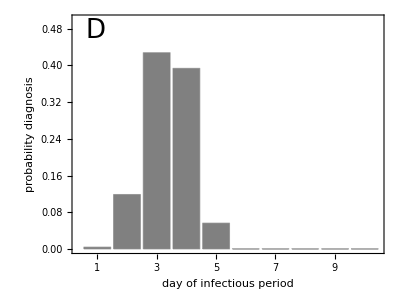

```mathematica
figure1d=Show[BarChart[probbeingdiagnosed[[1]], PlotRange->{All,{0,0.5}}, AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5], FrameStyle->Directive[Black,17],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}],Graphics[Text[StyleForm["D",FontSize->26],{(10.0-0.5)*0.1,0.5*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_1D_",date,".pdf"],figure1d,"pdf"];
```

```mathematica
Total[rzeroperc*(1-cumprobbeingdiagnosed)[[1]]]
```

45.6381

contact tracing and vaccination:

```mathematica
timewindow=infectious;
```

probability of being diagnosed on day i, if one has not been diagnosed up to day j (i>j):

```mathematica
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
sums=Table[∑_(k=1)^(infectious-j) pd[[1,j,k]],{j,1,infectious-1}]
```

{1.,1.,1.,1.,0.974785,0.821536,0.547714,0.282691,0.101183}

```mathematica
BarChart[sums, ChartStyle->{GrayLevel[0.8]},ChartLabels->Table[i,{i,1,infectious}],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{Automatic,Automatic,None,None}];
```

```mathematica
probvacc[vd_,cv_]:=Table[Flatten[{Table[∑_(j=i)^Min[i-1+Length[pd[[ds,i]]],i+timewindow-vd] pd[[ds,i,j-i+1]]*cv,{i,1,infectious-1}],0}],{ds,1,infectious}];
```

probability of a contact being vaccinated by day since first symptoms of source (probvacc2: source is secondary case, contact is ring 1; probvacc3: source is secondary case, contact is ring 2):

effective reproduction ratio with diagnosis probability  as above for all infecteds:

```mathematica
reffiso[pt_,ds_]:=∑_(i=1)^infectious ((Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

effective reproduction ratio with ringvaccination:

```mathematica
reffvacc1[pt_,vd1_,vd2_,cv1_,cv2_,ds_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probvacc[vd1,cv1][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc2[pt_,vd1_,vd2_,cv1_,cv2_,ds_]:=∑_(i=1)^infectious ( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probvacc[vd2,cv2][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc[pt_,vd1_,vd2_,cv1_,cv2_,ds_]:=reffvacc1[pt,vd1,vd2,cv1,cv2,ds]+reffvacc2[pt,vd1,vd2,cv1,cv2,ds]
```

## Exponential growth rate and doubling time

```mathematica
generationseff[r_,pt_,vd1_,vd2_,cv1_,cv2_,ds_]:=∑_(i=1)^infectious Sum[Exp[-r*(i+k)]*startinf[[k]]*((Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probvacc[vd1,cv1][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))+( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probvacc[vd2,cv2][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))),{k,1,latent}];
```

```mathematica
expgrowtheff[pt_,vd1_,vd2_,cv1_,cv2_,ds_]:=FindRoot[generationseff[r,pt,vd1,vd2,cv1,cv2,ds]==1,{r,1}][[1,2]]
```

```mathematica
doublingtimeeff[pt_,vd1_,vd2_,cv1_,cv2_,ds_]:=Log[2]/expgrowtheff[pt,vd1,vd2,cv1,cv2,ds];
```

## Specific parameter values

```mathematica
vaccdelay2=1.0;vaccdelay3=1.0;coverage2=1.0; coverage3=1.0;diagdelay=1;
```

```mathematica
reffiso[transmissibility,diagdelay]
```

1.54894

```mathematica
reffvacc1[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay]
```

0.000126302

```mathematica
reffvacc2[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay]
```

0.000226994

```mathematica
reffvacc[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay]
```

0.000353296

```mathematica
expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay]
```

-1.13857

```mathematica
doubeff=doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay]
```

-0.60879

```mathematica
doubincrease=doubeff/unconstraineddoubtime
```

-0.169716

```mathematica
xdata=Table[rzero[pt],{pt,0,0.4,0.05}]
```

{0.,0.823595,1.64719,2.47078,3.29438,4.11797,4.94157,5.76516,6.58876}

```mathematica
ydata0=Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.1,diagdelay],{pt,0,0.4,0.05}],{cv,1,11}];
```

```mathematica
figure1=Transpose[Prepend[ydata0,xdata]];
```

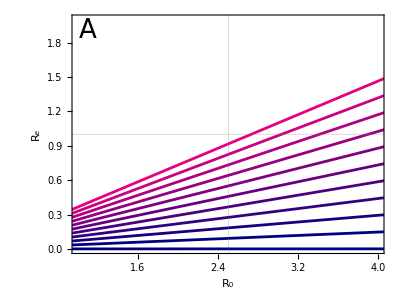

```mathematica
figure2a=Show[Show[Table[ListPlot[Transpose[{xdata,ydata0[[k]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[1-k*0.1,0,0.5],Thickness[0.005]}],{k,1,11}], PlotRange->{{1,4},{0,2}}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},{{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,e]],None},{Text[Subscript[R,0]],"Varying tracing coverage"}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["A",FontSize->26],{1.0+0.1,2.0*0.95}]]]
```

```mathematica
ydata1=Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,coverage3,dd],{pt,0,0.4,0.05}],{dd,1,10}];
```

```mathematica
figure2=Transpose[Prepend[ydata1,xdata]];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Reff0_",date,".pdf"],plot0,"pdf"];
```

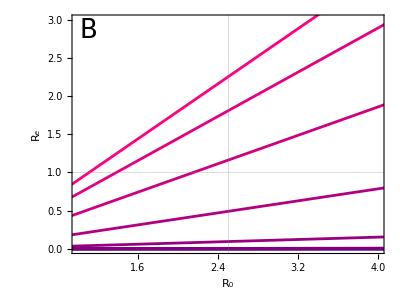

```mathematica
figure2b=Show[Show[Table[ListPlot[Transpose[{xdata,ydata1[[k]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[k*0.1,0.0,0.5],Thickness[0.005]} ],{k,1,10}], PlotRange->{{1,4},{0,3}}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},{{1,{Red,Thickness[0.007]}}}}, Frame->True,FrameStyle->Directive[Black,17], FrameLabel->{{ Text[Subscript[R,e]],None},{Text[Subscript[R,0]],"Varying diagnosis delay"}},  FrameTicks->{Automatic, Automatic, None, None}], Graphics[Text[StyleForm["B",FontSize->26],{1.0+0.1,3.0*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Reff1_",date,".pdf"],plot1,"pdf"];
```

```mathematica
Show[GraphicsRow[{plot1,plot0}], DisplayFunction->$DisplayFunction, GraphicsSpacing->0.01];
```

```mathematica
xdata2=Table[rzero[pt],{pt,0.01,0.5,0.001}];
```

```mathematica
critcov2=Table[Table[Part[FindRoot[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,cv2,j]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.001}],{j,1,10}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
figure3=Transpose[Prepend[critcov2,xdata2]];
```

```mathematica
figurecritcov1=Show[Table[ListPlot[Transpose[{xdata2,critcov2[[j]]}], Joined->True,PlotRange->{{0,5},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.4,0], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],Red}},None}],{j,1,10}], Frame->True,FrameLabel->{"R0", "fraction isolated"},  FrameTicks->{Automatic, Automatic, None, None},PlotLabel->"Varying time to diagnosis",FrameStyle->Directive["Label",16]];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/CritCov1_",date,".pdf"],figurecritcov1,"pdf"];
```

```mathematica
xdata3=Table[rzero[pt],{pt,0.01,0.5,0.001}];
```

```mathematica
critcov3=Table[Table[Part[FindRoot[reffvacc[pt,vaccdelay2,j,coverage2,cv2,diagdelay]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.001}],{j,1,10}];
```

```mathematica
figure4=Transpose[Prepend[critcov3,xdata3]];
```

```mathematica
figurecritcov2=Show[Table[ListPlot[Transpose[{xdata3,critcov3[[j]]}], Joined->True,PlotRange->{{0,5},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.4,0], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],Red}},None}],{j,1,10}], Frame->True, FrameLabel->{"R0","fraction isolated"},FrameStyle->Directive["Label",16],FrameTicks->{Automatic, Automatic, None,None},PlotLabel->"Varying time to trace non-household contacts"];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Critcov2_",date,".pdf"],figurecritcov2,"pdf"];
```

## Scenarios asymptomatic infection

```mathematica
fractionsymptomatic={};ydata00={};ydata11={};critcov22={};critcov33={};growthrate={};doubtime={};
growthrate2={};
doubtime2={};
```

```mathematica
scenarios=Length[scenarioasymptomatic];
```

```mathematica
Do[ factorasymptomatic=scenarioasymptomatic[[l]]; 
 probsymp= Table[factorasymptomatic*sympconstant*PDF[GammaDistribution[gamma1,gamma2],tau], {tau,1,infectious}];probdevelopingsymptoms=Table[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],{i,1,infectious}];fraccas=Total[probdevelopingsymptoms];fractionsymptomatic=Append[fractionsymptomatic,fraccas];probdiag=Table[Table[If[i<ds ,0.0,probsymp[[i]]],{i,1,infectious}],{ds,1,infectious}];pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];ydata00=Append[ydata00,Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.1,diagdelay],{pt,0,0.4,0.05}],{cv,1,11}]];ydata11=Append[ydata11,1Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,coverage3,dd],{pt,0,0.4,0.05}],{dd,1,3}]];critcov22=Append[critcov22,Table[Table[Part[FindRoot[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,cv2,j]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.001}],{j,1,10}]];critcov33=Append[critcov33,Table[Table[Part[FindRoot[reffvacc[pt,vaccdelay2,j,coverage2,cv2,diagdelay]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.001}],{j,1,7}]];growthrate=Append[growthrate,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd],{dd,1,10}]];doubtime=Append[doubtime,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd],{dd,1,10}]];
growthrate2=Append[growthrate2,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.1,diagdelay],{cv,1,11}]];doubtime2=Append[doubtime2,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.1,diagdelay],{cv,1,11}]],{l,Length[scenarioasymptomatic]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fractionsymptomatic[[2]]
```

0.95

```mathematica
legendtext=Table[ToString[Round[100*fractionsymptomatic[[i]]]],{i,1,Length[fractionsymptomatic]}]
```

{100,95,90,85,80,75,70,65,60,55,50,45,40,35,30,25,20,15,10,5}

```mathematica
ydata00;
```

```mathematica
ydata11;
```

```mathematica
critcov22 ;
```

```mathematica
Length[critcov33 [[1,1]]]
```

491

```mathematica
figurereff00=Show[Table[ListPlot[Transpose[{xdata,ydata00[[k,10]]}],Joined->True,PlotStyle->{RGBColor[k*0.1,0.4,0],Thickness[0.005]}],{k,1,scenarios}], PlotRange->{{0,5},{0,3}}, GridLines->{{rzero[transmissibility]},{{1,Red}}},Frame->True, FrameLabel->{"R0", "R_e"},  PlotLabel->"Varying proportion asymptomatic", FrameTicks->{Automatic, Automatic, None, None}, FrameStyle->Directive["Label",16]];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Re_asymptomatic_",date,".pdf"],figureeff00,"pdf"];
```

```mathematica
figurereff11=Show[Table[ListPlot[Transpose[{xdata,ydata11[[k,diagdelay]]}],Joined->True,PlotStyle->{RGBColor[k*0.1,0.4,0],Thickness[0.005]} ],{k,1,scenarios}], PlotRange->{{0,5},{0,3}}, GridLines->{{rzero[transmissibility]},{{1,Red}}}, Frame->True, FrameLabel->{"R0", "R_e"}, FrameTicks->{Automatic, Automatic, None, None},PlotLabel->"Varying proportion asymptomatic",FrameStyle->Directive["Label",16]];
```

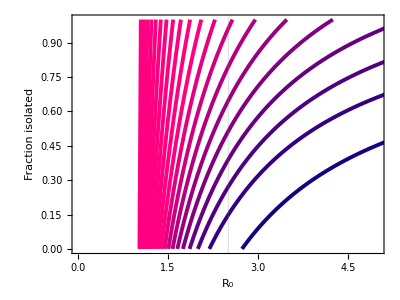

```mathematica
figurecritcov22=Show[Table[ListPlot[Transpose[{xdata3,critcov22[[j,1]]}], Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{{0,5},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.0,0.5], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},None}],{j,1,scenarios}], Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{{ Text[Fraction isolated],None},{Text[Subscript[R,0]],"Varying fraction asymptomatic"}},FrameTicks->{Automatic, Automatic, None,None} ]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Critcov_asymptomatic_",date,".pdf"],figurecritcov22,"pdf"];
```

```mathematica
scennumber={1,5,9};
```

```mathematica
graphlabels={ToString[A],ToString[C],ToString[E]};
```

```mathematica
graphlabels2={ToString[B],ToString[D],ToString[F]};
```

```mathematica
xlabels=Text[ Style[#,Large]]&/@{"Varying diagnosis delay","Varying tracing delay"};
ylabels=Text[Style[#,Large]]&/@Table[StringJoin[legendtext[[scennumber[[k]]]],"% asymptomatic"],{k,1,3}];
```

```mathematica
legend2={LineLegend[ Table[RGBColor[k 0.1,0.0,0.5],{k,1,10}],Table[j,{j,1,10}],LegendLabel->"diagnosis delay (days)",LabelStyle->Directive[Black,14], LegendMargins->5],None,None,None,None};
```

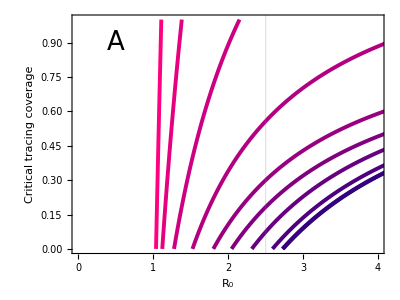
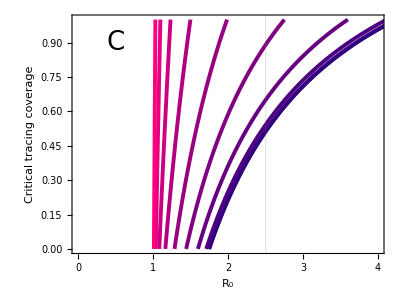
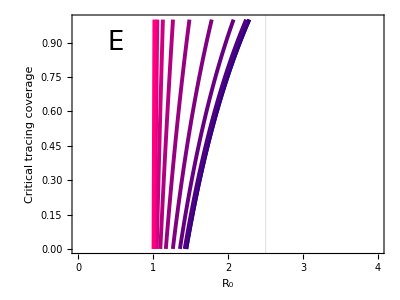

```mathematica
figure3firstpanel=Table[Show[Show[Table[ListPlot[Transpose[{xdata3,critcov22[[scennumber[[k]],j]]}], Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{{0.0,4},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.0,0.5], Thickness[0.007]}, (*PlotLegends->Placed[legend2[[k]],Right],*)GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},None}],{j,1,10}],Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{{ Text["Critical tracing coverage"],None},{Text[Subscript[R,0]],StringJoin[(*"Varying diagnosis delay, ",*) legendtext[[scennumber[[k]]]],"% symptomatic"]}},FrameTicks->{Automatic, Automatic, None,None} ],Graphics[Text[StyleForm[graphlabels[[k]],FontSize->26],{0.5,1.0*0.9}]]],{k,1,3}]
```

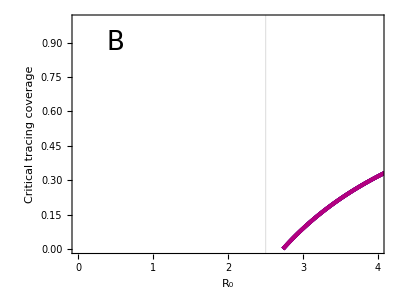
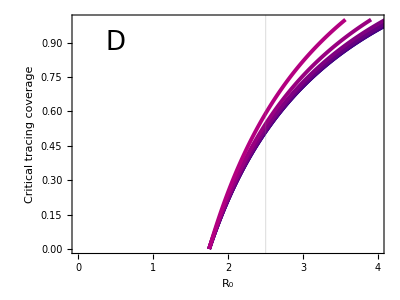
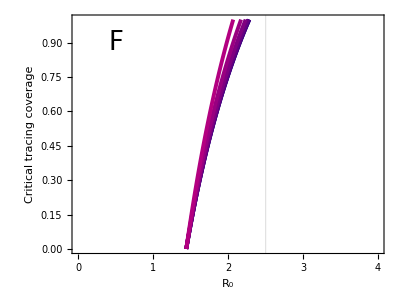

```mathematica
figure3secondpanel=Table[Show[Show[Table[ListPlot[Transpose[{xdata3,critcov33[[scennumber[[k]],j]]}], Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{{0,4},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.0,0.5], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},None}],{j,1,7}], Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{{ Text["Critical tracing coverage"],None},{Text[Subscript[R,0]],StringJoin[(*"Varying tracing delay, ",*) legendtext[[scennumber[[k]]]],"% symptomatic"]}},FrameTicks->{Automatic, Automatic, None,None}  ],Graphics[Text[StyleForm[graphlabels2[[k]],FontSize->26],{0.5,1.0*0.9}]]],{k,1,3}]
```

```mathematica
xdata3;
```

```mathematica
xvalue=Take[Flatten[Position[xdata3,SelectFirst [xdata3, #>rzero[transmissibility]&]]-1],1] [[1]]
```

143

```mathematica
xvalues=Table[Take[Flatten[Position[xdata3,SelectFirst [xdata3, #>1.0+k*0.5&]]-1],1] [[1]],{k,1,5}]
```

{82,112,142,173,203}

```mathematica
xdata3[[xvalues]]
```

{1.49894,1.9931,2.48726,2.99789,3.49204}

```mathematica
xdata3[[xvalue+1]]
```

2.5202

```mathematica
rzero[transmissibility]
```

2.50373

```mathematica
critcov33[[2,1,xvalue]]
```

0.148086

```mathematica
coverages=Table[Table[{fractionsymptomatic[[j]],Max[0.0,Min[1.0,critcov33[[j,1,xvalues[[k]]]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,scenarios}],{k,1,5}];
```

```mathematica
legendlabels=NumberForm[Table[1.0+0.5*k,{k,1,5}],{2,1}]
```

{1.5,2.0,2.5,3.0,3.5}

```mathematica
legend={LineLegend[ Table[RGBColor[k 0.2,0.0,0.5],{k,1,5}],coverages[[All,1,3]],LegendLabel->"R_0",LabelStyle->Directive[Black,14], LegendMargins->5],None,None,None,None};
```

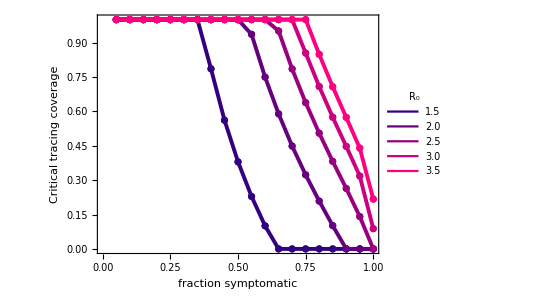

```mathematica
figure4a=Show[Show[Table[ListPlot[ Table[{fractionsymptomatic[[j]],Max[0.0,Min[1.0,critcov33[[j,1,xvalues[[k]]]]]]},{j,1,scenarios}],Joined->True,Mesh->Full,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[k 0.2,0.0,0.5], Thickness[0.007]}, PlotLegends->Placed[legend[[k]],{0.15,0.4}], Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"fraction symptomatic","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,1,5}]](*,Graphics[Text[StyleForm["A",FontSize->26],{0.95,1.0*0.95}]]*)]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Fracisolate_asymptomatic_",date,".pdf"],figfracisolate,"pdf"];
```

```mathematica
growthrate[[1,1]]
```

-1.13857

```mathematica
figexpgrowth=ListPlot[ Table[Table[{fractionsymptomatic[[j]],growthrate[[j,k]]},{j,1,scenarios}],{k,1,10}],PlotStyle->Table[{RGBColor[k 0.1,0.4,0], Thickness[0.007]},{k,1,10}],Joined->True, PlotRange->{{0.5,1.0},All},Frame->True,FrameLabel->{"fraction symptomatic","exponential growth rate"},PlotLabel->"Varying time to diagnosis"];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Expgrowth_asymptomatic_",date,".pdf"],figexpgrowth,"pdf"];
```

```mathematica
doubtime;
```

```mathematica
ListPlot[ Table[Table[{fractionsymptomatic[[j]],doubtime[[j,k]]},{j,1,scenarios}],{k,1,5}],PlotRange->{{0,1},{-20,100}},Joined->True,Mesh->Full,Frame->True,FrameLabel->{"fraction symptomatic","doubling time"}];
```

```mathematica
ydata11[[1,1,3]]
```

0.000232431

```mathematica
growthrate[[1]]
```

{-1.13857,-1.13803,-1.1207,-1.0289,-0.738765,-0.332497,-0.119115,0.0286616,0.119905,0.169024}

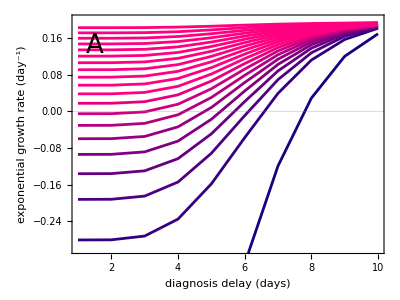

```mathematica
figure5a=Show[Show[Table[ListPlot[Transpose[{Table[k,{k,1,10}],growthrate[[j]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[j*0.1,0.0,0.5],Thickness[0.005]}],{j,1,scenarios}], PlotRange->{{1,10},{-0.3,0.2}},GridLines->{None,{{0,{Red,Thickness[0.007]}}}},PlotRange->{{1,10},All},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"diagnosis delay (days)", "exponential growth rate (day^-1)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["A",FontSize->26],{1.0+0.5,0.15*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Expgrowth_diagdelay_asymptomatic_",date,".pdf"],figureexpgrowth,"pdf"];
```

```mathematica
Table[Max[0.0,doubtime[[1,i]]],{i,1,Length[doubtime[[1]]]}]
```

{0.,0.,0.,0.,0.,0.,0.,24.1838,5.78079,4.10089}

```mathematica
doubtimepos=Transpose[Table[Table[If[doubtime[[j,k]]>0,doubtime[[j,k]],100],{j,1,Length[scenarioasymptomatic]}],{k,1,10}]];
```

```mathematica
legendsymp=LineLegend[Table[RGBColor[j*0.1,0.0,0.5],{j,1,scenarios}],Table[legendtext[[j]],{j,1,scenarios}],LegendLabel->"% symptomatic",LabelStyle->Directive[Black,10], LegendMargins->5];
```

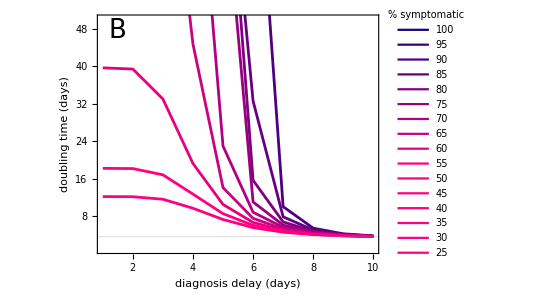

```mathematica
figure5b=Show[Show[Table[ListPlot[Transpose[{Table[k,{k,1,10}], doubtimepos[[j]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize, PlotStyle->{RGBColor[j*0.1,0.0,0.5],Thickness[0.005]}],{j,3,scenarios}],   PlotRange->{{1,10},{1,50}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"diagnosis delay (days)", "doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["B",FontSize->26],{1.0+0.5,50*0.95}]],Graphics[Inset[legendsymp,{8.5,30}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Doubtime_diagdelay_asymptomatic_",date,".pdf"],figuredoubtime,"pdf"];
```

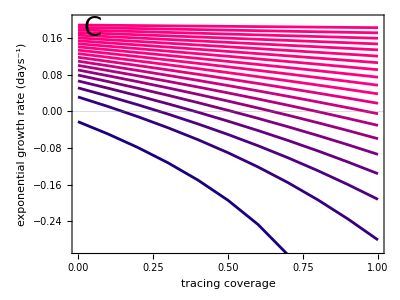

```mathematica
figure5c=Show[Show[Table[ListPlot[Transpose[{Table[(k-1)*0.1,{k,1,11}],growthrate2[[j]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[j*0.1,0.0,0.5],Thickness[0.005]}],{j,1,scenarios}],  GridLines->{None,{{0,{Red,Thickness[0.007]}}}},PlotRange->{{0,1},{-0.3,0.2}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"tracing coverage", "exponential growth rate (days^-1)"},  (*PlotLabel->"Varying proportion asymptomatic", *)FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["C",FontSize->26],{0.05,0.2*0.9}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Expgrowth_traced_asymptomatic_",date,".pdf"],figureexpgrowth2,"pdf"];
```

```mathematica
doubtimepos2=Transpose[Table[Table[If[doubtime2[[j,k]]>0,doubtime2[[j,k]],100],{j,1,Length[scenarioasymptomatic]}],{k,1,11}]];
```

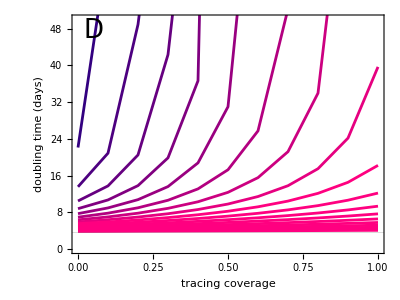

```mathematica
figure5d=Show[Show[Table[ListPlot[Transpose[{Table[(k-1)*0.1,{k,1,11}],doubtimepos2[[j]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[j*0.1,0.0,0.5],Thickness[0.005]}],{j,1,scenarios-1}],   PlotRange->{{0,1},{0,50}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"tracing coverage", "doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["D",FontSize->26],{0.0+0.05,50*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Doubtime_traced_asymptomatic_",date,".pdf"],figuredoubtime2,"pdf"];
```

## Scenarios reduced contact rate

```mathematica
ydata000={};ydata111={};critcov222={};critcov333={};growthrate3={};doubtime3={};
growthrate4={};growthrate5={};
doubtime4={};doubtime5={};reffredcontact={};
scenarios=Length[scenariocontactred];
```

```mathematica
factorasymptomatic=scenarioasymptomatic[[10]];probsymp=Array[f,infectious];
 probsymp=Table[ factorasymptomatic*sympconstant*PDF[GammaDistribution[gamma1,gamma2],tau] ,{tau,1,infectious}];probdevelopingsymptoms=Table[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],{i,1,infectious}];fraccas=Total[probdevelopingsymptoms];fractionsymptomatic=Append[fractionsymptomatic,fraccas];probdiag=Table[Table[If[i<ds ,0.0,probsymp[[i]]],{i,1,infectious}],{ds,1,infectious}];pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
contactreduction1=1.0;contactreduction2=1.0;mu2=negbinn*saturation2*contactreduction2 ;transmissibility=0.152;
 For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}]; 
xdata4=Table[{pt,rzero[pt]},{pt,0.01,0.5,0.001}];
xvalues2=Table[Take[Flatten[Position[xdata4[[All,2]],SelectFirst [xdata4[[All,2]], #>1.0+k*0.5&]]-1],1] [[1]],{k,1,5}];
xdata4[[xvalues2]];
```

```mathematica
Do[transmissibility=xdata4[[xvalues2]][[n,1]];reffredcontact=Append[reffredcontact,rzero[transmissibility]];Do[ contactreduction2=scenariocontactred[[l]];mu1=meanhouseholdcontacts*saturation1*contactreduction1;
mu2=negbinn*saturation2*contactreduction2 ;
contactdist1=Array[f,infectious];contactdist2=Array[f,infectious];
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}]; probdiag=Table[Table[If[i<ds ,0.0,probsymp[[i]]],{i,1,infectious}],{ds,1,infectious}];pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];reffredcontact=Append[reffredcontact,rzero[transmissibility]];critcov222=Append[critcov222,Table[Part[FindRoot[reffvacc[transmissibility,vaccdelay2,vaccdelay3,cv1,0,j]==1, {cv1,0.5}],1,2],{j,1,1}]];critcov333=Append[critcov333,Table[Part[FindRoot[reffvacc[transmissibility,vaccdelay2,j,coverage2,cv2,diagdelay]==1, {cv2,0.5}],1,2],{j,1,1}]];growthrate3=Append[growthrate3,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd],{dd,1,10}]]; doubtime3=Append[doubtime3,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd],{dd,1,10}]];
growthrate4=Append[growthrate4,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.1,diagdelay],{cv,1,11}]];growthrate5=Append[growthrate5,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.1,0.0,diagdelay],{cv,1,11}]];
doubtime4=Append[doubtime4,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.1,diagdelay],{cv,1,11}]];doubtime5=Append[doubtime5,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.1,0.0,diagdelay],{cv,1,11}]],{l,1,Length[scenariocontactred]}],{n,1,5}]
```

```mathematica
legendtext=Table[ToString[Ceiling[100*scenariocontactred[[i]]]],{i,1,Length[scenariocontactred]}];
```

```mathematica
coverageshousehold=Table[Table[{scenariocontactred[[j]],Max[0.0,Min[1.0,critcov222[[(k-1)*Length[scenariocontactred]+j,1]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,Length[scenariocontactred]}],{k,1,5}];
```

```mathematica
legend2={LineLegend[ Table[RGBColor[k 0.2,0.5,0.0],{k,1,5}],coverageshousehold[[All,1,3]],LegendLabel->"R_0",LabelStyle->Directive[Black,14], LegendMargins->5],None,None,None,None};
```

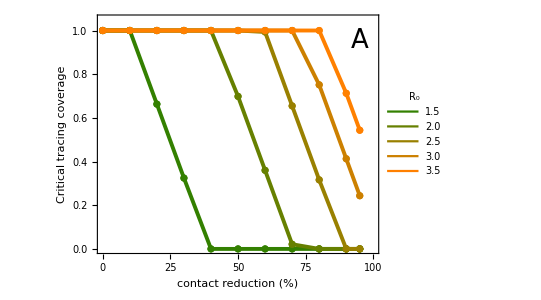

```mathematica
figure7a=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverageshousehold[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.05}},Joined->True,Mesh->Full,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[k 0.2,0.5,0.0], Thickness[0.007]}, PlotLegends->Placed[legend2[[k]],{0.1,0.35}], Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"contact reduction (%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,1,5}]],Graphics[Text[StyleForm["A",FontSize->26],{100-5,1.0*0.95}]]]
```

```mathematica
coverages=Table[Table[{scenariocontactred[[j]],Max[0.0,Min[1.0,critcov333[[(k-1)*Length[scenariocontactred]+j,1]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,Length[scenariocontactred]}],{k,1,5}];
```

```mathematica
reffredcontact;
```

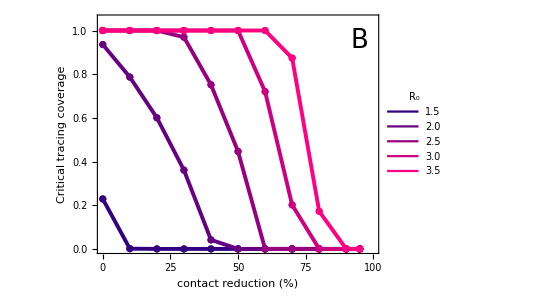

```mathematica
figure7b=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverages[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.05}},Joined->True,Mesh->Full,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[k 0.2,0.0,0.5], Thickness[0.007]}, PlotLegends->Placed[legend[[k]],{0.9,0.4}], Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"contact reduction (%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,1,5}]],Graphics[Text[StyleForm["B",FontSize->26],{100-5,1.0*0.95}]]]
```

```mathematica
growthrate3[[50]]
```

{0.0317067,0.0318072,0.0348386,0.0482538,0.075081,0.108877,0.139804,0.162286,0.176157,0.18376}

```mathematica
figure6aa=Show[Show[Table[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,growthrate5[[(k-1)*scenarios+j,i]]},{j,1,scenarios}],PlotRange->{{0,100},{-0.06,0.1}},Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i 0.1,0.5,0.0], Thickness[0.007]}, Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"contact reduction (%)","growth rate (days^-1)"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}],{i,1,11}]],Graphics[Text[StyleForm["A",FontSize->26],{85,0.1*0.85}]]];
```

```mathematica
figure6ab=Show[Show[Table[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,growthrate4[[(k-1)*scenarios+j,i]]},{j,1,scenarios}],PlotRange->{{0,100},{-0.06,0.1}},Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i 0.1,0.0,0.5], Thickness[0.007]}, Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"contact reduction (%)","growth rate (days^-1)"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}],{i,1,11}]](*,Graphics[Text[StyleForm["A",FontSize->26],{5,0.1*0.85}]]*)];
```

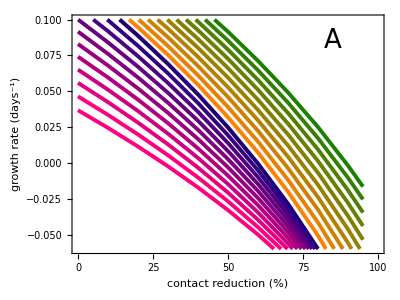

```mathematica
figure6a=Show[figure6aa,figure6ab]
```

```mathematica
doubtime3;
```

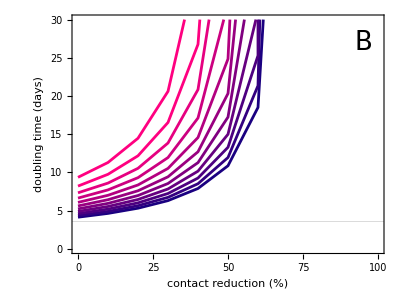

```mathematica
figure6ac=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,If[doubtime4[[3*scenarios+j,i]]>0,doubtime4[[3*scenarios+j,i]],70]},{j,1,scenarios}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i*0.1,0.0,0.5],Thickness[0.005]},   PlotRange->{{0,100},{0,30}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"contact reduction (%)", "doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],{i,1,11}],Graphics[Text[StyleForm["B",FontSize->26],{95,30*0.9}]]]]
```

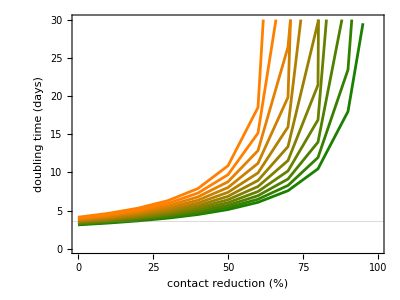

```mathematica
figure6ad=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,If[doubtime5[[3*scenarios+j,i]]>0,doubtime5[[3*scenarios+j,i]],70]},{j,1,scenarios}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i*0.1,0.5,0.0],Thickness[0.005]},   PlotRange->{{0,100},{0,30}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"contact reduction (%)", "doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],{i,1,11}](*,Graphics[Text[StyleForm["D",FontSize->26],{0.0+0.05,50*0.95}]]*)]]
```

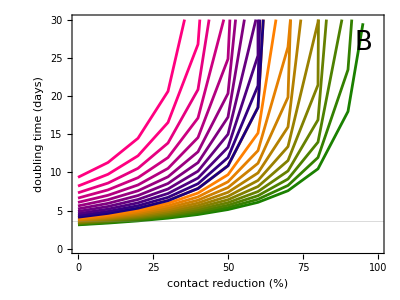

```mathematica
figure6b=Show[figure6ad,figure6ac]
```

```mathematica
contactreduction1=1.0;contactreduction2=1.0;negbinp=0.5;mu2=negbinn*saturation2*contactreduction2 ;transmissibility=0.152;
 For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}]; 
xdata4=Table[{pt,rzero[pt]},{pt,0.01,0.5,0.001}];
xvalues2=Table[Take[Flatten[Position[xdata4[[All,2]],SelectFirst [xdata4[[All,2]], #>1.0+k*0.5&]]-1],1] [[1]],{k,1,5}];
xdata4[[xvalues2]];
```

```mathematica
densityplot=DensityPlot[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,(cv1-1)*0.01,(cv2-1)*0.01,diagdelay],{cv1,1,100},{cv2,1,100},PlotLegends->Automatic,Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"coverage household","coverage non-household"}];
```

```mathematica
contourplot=ContourPlot[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,(cv1-1)*0.01,(cv2-1)*0.01,diagdelay],{cv1,1,100},{cv2,1,100},Contours->{0},ContourShading->None,ContourStyle->Directive[Red,Thick], ContourLabels->None,Frame->True,FrameLabel->{"coverage household","coverage non-household"}];
```

```mathematica
figure8=Show[{densityplot,contourplot}, ImageSize->ImSize,FrameStyle->Directive[Black,17]];
```

## Output

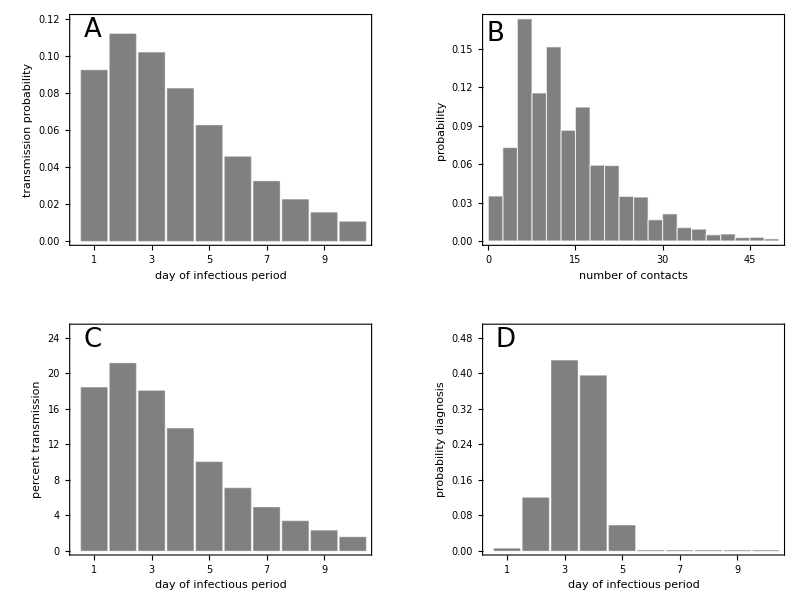

```mathematica
figure1=Show[GraphicsGrid[{{figure1a,figure1b},{figure1c,figure1d}},ImageSize->2*ImSize]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_1_",date,".pdf"],figure1,"pdf"];
```

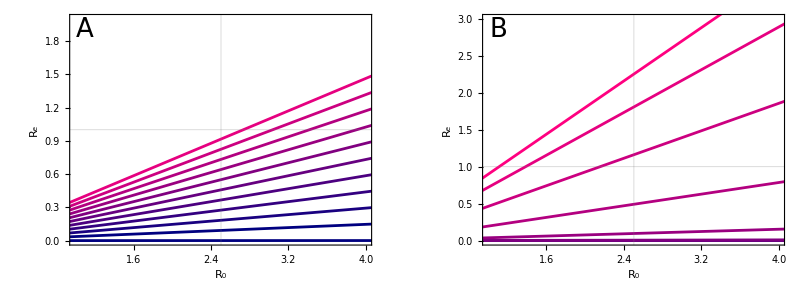

```mathematica
figure2=Show[GraphicsRow[{figure2a,figure2b}],ImageSize->2*ImSize]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_2_",date,".pdf"],figure2,"pdf"];
```

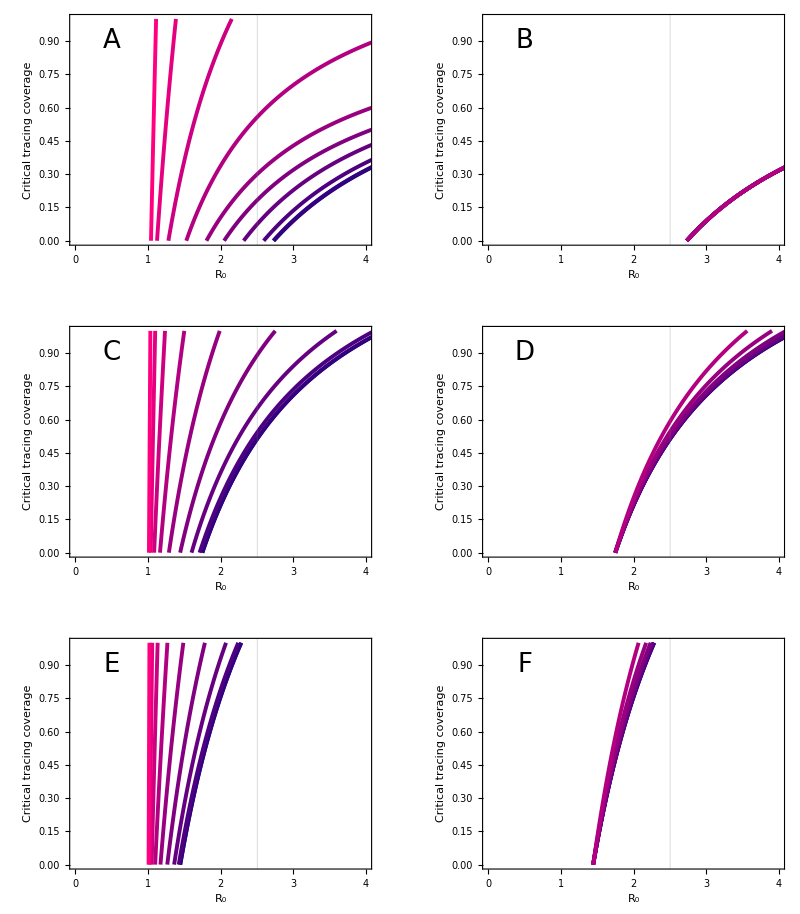

```mathematica
figure3=Show[GraphicsGrid[Transpose[{figure3firstpanel,figure3secondpanel}],ImageSize->2*ImSize]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_3_",date,".pdf"],figure3,"pdf"];
```

```mathematica
figure4=Show[figure4a]
```

-Graphics-

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_4_",date,".pdf"],figure4,"pdf"];
```

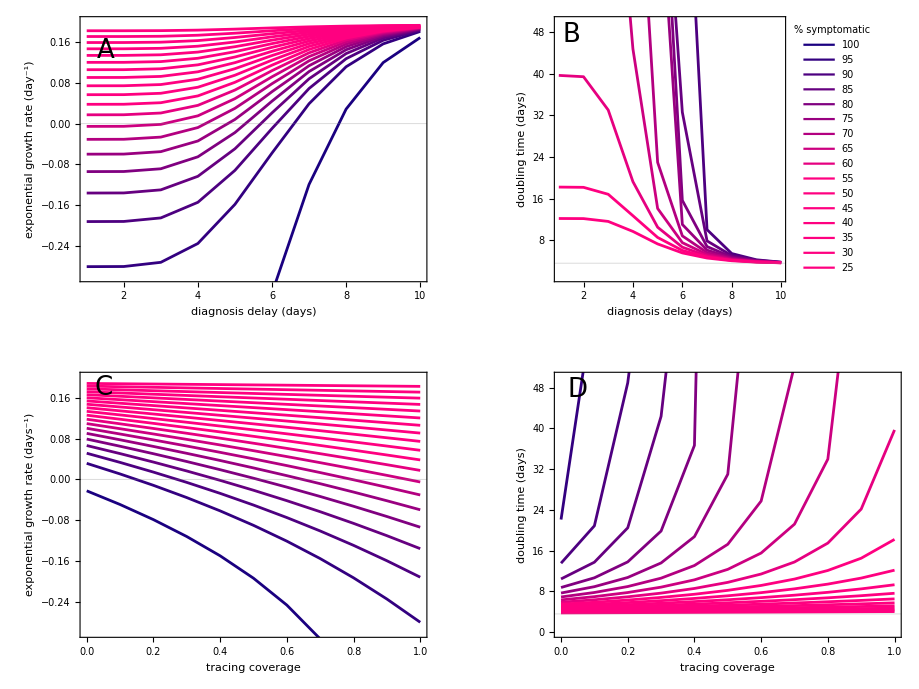

```mathematica
figure5=Show[Show[GraphicsGrid[{{figure5a,figure5b},{figure5c,figure5d}},ImageSize->2.3*ImSize]](*,PlotLabel->"Varying proportion asymptomatic"*)]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_5_",date,".pdf"],figure5,"pdf"];
```

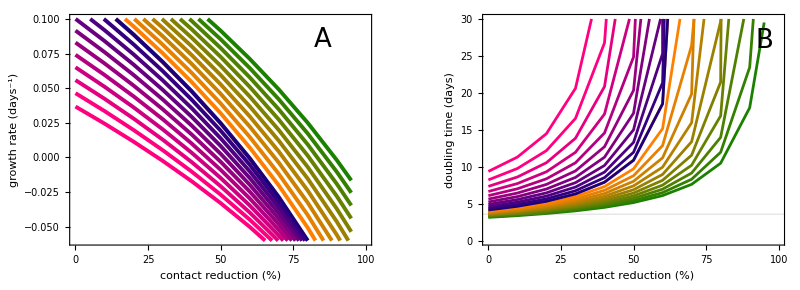

```mathematica
figure6=Show[GraphicsRow[{figure6a,figure6b},ImageSize->2*ImSize]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_6_",date,".pdf"],figure6,"pdf"];
```

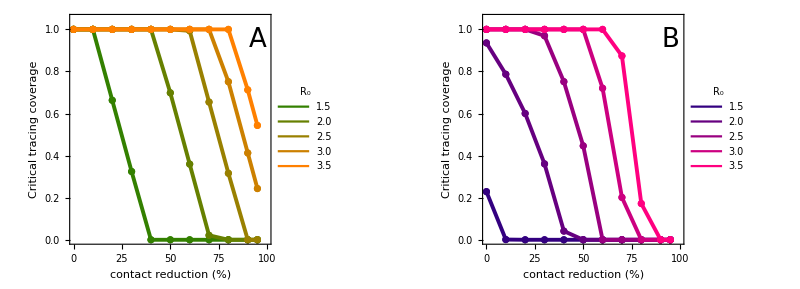

```mathematica
figure7=Show[GraphicsRow[{figure7a,figure7b},ImageSize->2*ImSize]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_7_",date,".pdf"],figure7,"pdf"];
```

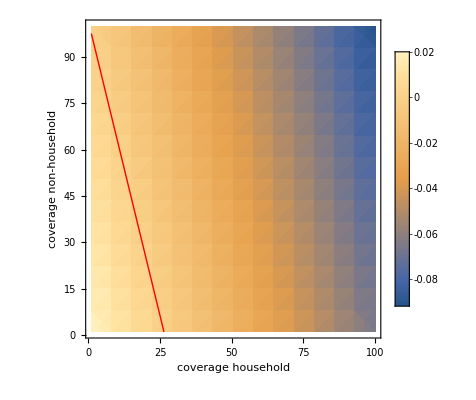

```mathematica
figure8=Show[{densityplot,contourplot}, ImageSize->ImSize,FrameStyle->Directive[Black,17]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_8_",date,".pdf"],figure8,"pdf"];
```